```mathematica
Quit
```

```mathematica
ClearAll
```

ClearAll

```mathematica
M=1;α=3/10;
```

```mathematica
f[r_]:=1-(2M ⅇ^((-α M^(2/3))/r^2))/r;
```

```mathematica
g[u_]:=1-2 M u ⅇ^(-u^2 α M^(2/3));
```

```mathematica
event=NSolve[f[r]==0,r]
```

NSolve::ifun: NSolve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{r→0.447692},{r→1.82833}}

```mathematica
ev=event[[2,1,2]];
```

```mathematica
Solve[r^2-bc^2 f[r]==0&&2 bc^2 f[r]^2-r^3 D[f[r],r]==0&&2<r<3&&5<bc<6,{bc,r},Reals]
```

{{bc→Root5.01Root[{{-2 #1^2+ⅇ^(3/(10 #2^2)) #1^2 #2-ⅇ^(3/(10 #2^2)) #2^3&,20 #1^2+3 ⅇ^(3/(10 #2^2)) #2-20 ⅇ^(3/(10 #2^2)) #1^2 #2+5 ⅇ^(3/(5 #2^2)) #1^2 #2^2-5 ⅇ^(3/(10 #2^2)) #2^3&},{5.00833032580966815,2.81573699069825915}},1]5.008330325809668,r→Root2.82Root[{{-2 #1^2+ⅇ^(3/(10 #2^2)) #1^2 #2-ⅇ^(3/(10 #2^2)) #2^3&,20 #1^2+3 ⅇ^(3/(10 #2^2)) #2-20 ⅇ^(3/(10 #2^2)) #1^2 #2+5 ⅇ^(3/(5 #2^2)) #1^2 #2^2-5 ⅇ^(3/(10 #2^2)) #2^3&},{5.00833032580966815,2.81573699069825915}},2]2.8157369906982592}}

```mathematica
sol=N[%]
```

{{bc→5.00833,r→2.81574}}

```mathematica
ss=sol[[1,1,2]]
```

5.00833

```mathematica
sss=sol[[1,2,2]]
```

2.81574

```mathematica
l[b0_]:=Module[{b=b0},FindInstance[1/b^2-x^2 g[x]==0&&0.36>x>0,{x},Reals]]
```

```mathematica
ϕ[b_]:=NIntegrate[1/Sqrt[1/b^2-x^2  g[x]],{x,0,l[b][[1,1,2]]}]
```

```mathematica
ψ[b_]:=NIntegrate[1/Sqrt[1/b^2-x^2 g[x]],{x,0,1/ev}]
```

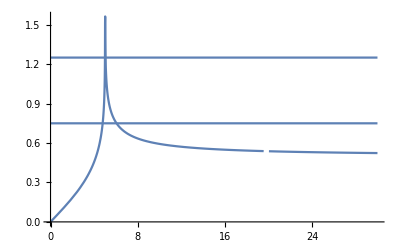

```mathematica
Plot[Piecewise[{{{ψ[b]/(Pi 2),3/4,5/4},0.001<b<ss},{{ϕ[b]/Pi,3/4,5/4},b>=ss}}],{b,0.001,30}]
```